# Cluster potentiation in truncated network

## Synapses and plasticity function

### Parameters

```mathematica
tausyn =10.0;
tauslow = 50.0;
taufast = 25;
ampfast = 0.08;
ampslow = -0.0533;
ρ = 0.002;
w = 0.7/12;
```

### Functions

```mathematica
plasticity[x_] = Piecewise[ {{ampfast*Exp[x/taufast]+ampslow*Exp[x/tauslow],x<0},{ampfast*Exp[-x/taufast]+ampslow*Exp[-x/tauslow],x>0}}]
synaptic[x_]= Piecewise[ {{0,x<0},{1/tausyn*Exp[-x/tausyn],x>0}}]
```

Piecewise[{{-0.0533 ⅇ^(0.02 x)+0.08 ⅇ^(x/25), x<0}, {0.08 ⅇ^(-x/25)-0.0533 ⅇ^(-0.02 x), x>0}, {0, True}}]

Piecewise[{{0, x<0}, {0.1 ⅇ^(-0.1 x), x>0}, {0, True}}]

```mathematica
fbar[ω_]= FourierTransform[plasticity[t],t,ω,FourierParameters->{1, -1}]
```

(-8.512×10^-7+0.004268 ω^2)/((6.4×10^-7+0. ⅈ)+(0.002+0. ⅈ) ω^2+1. ω^4)

```mathematica
synapticbar[ω_] = FourierTransform[synaptic[t],t,ω,FourierParameters->{1, -1}]
```

(0.+0.1 ⅈ)/((0.+0.1 ⅈ)-1. ω)

## ΔW coefficients

```mathematica
f0 = Re[fbar[0]];
fab[a_,b_] :=Re[1/(2*Pi)*NIntegrate[fbar[-x]*synapticbar[x]^a*synapticbar[-x]^b,{x,-Infinity,Infinity}]];
```

## Plots

```mathematica
tb[z_] := Total[Table[fab[j,z-j],{j,0,z}]];
convsums[t_,k_] := Exp[-Abs[t]/tausyn]/(2*k!)*(Abs[t]/tausyn)^k + 1/2*Exp[-Abs[t]/tausyn]*Total[Table[1/(j!)*(Abs[t]/tausyn)^j,{j,0,k}]]
```

```mathematica
plotlimit=ListPlot[Table[{z,tb[z]},{z,1,80}],PlotRange->All];
```

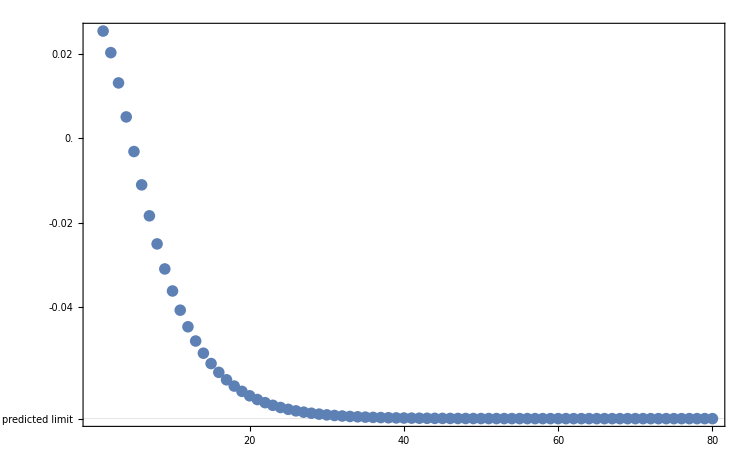

```mathematica
Show[plotlimit, BaseStyle ->{FontFamily ->  "Times",FontSize -> 15},AxesStyle->{White,Opacity[0]},TicksStyle -> {Opacity[1],24},Frame ->{True},FrameStyle -> Thick,FrameTicks->{{20,40,60,80},{{0.04,0.04},{0.02,0.02},{0.0,0.0},{-0.02,-0.02},{-0.04,-0.04},{Re[fbar[0]]/(2*tausyn),"predicted limit"}},None,None},FrameTicksStyle-> Directive[Black,24],GridLines->{{},{Re[fbar[0]]/(2*tausyn)}},GridLinesStyle->{Thick,Black}]
```

```mathematica
plotconvsums  = Plot[{10*plasticity[t],conv[t,4],conv[t,9],conv[t,19]},{t,-500,500},PlotLegends->{"F(t)","k=5","k=10","k=20"}];
```

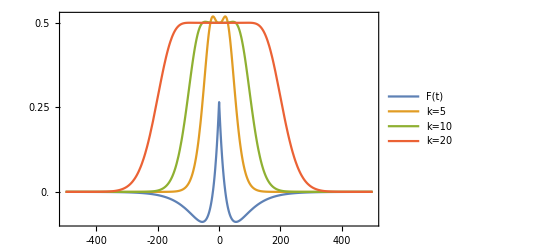

```mathematica
Show[plotconvsums,BaseStyle ->{FontFamily ->  "Times",FontSize -> 15},AxesStyle->None,TicksStyle -> {Opacity[1],24},Frame ->{True},FrameStyle -> Thick,FrameTicks->{{-400,-200,0,200,400},{0.0,0.25,0.5},None,None},FrameTicksStyle-> Directive[Black,24],PlotRange->Automatic]
```